## Figures: ROC curves for EWS in the Ricker model

## Import data

```mathematica
SetDirectory["/Users/tbury/Google Drive/Research/doctorate/critical_transitions_18/fisheries/roc_curves"];
```

```mathematica
(* ROC data *)
dfRocFold=Import["data/roc_fold.csv"];
dfRocFlip=Import["data/roc_flip.csv"];
```

## Figure params

```mathematica
(* colours *)
TMBcolours=ColorData[97,"ColorList"];
```

```mathematica
(* Figure params *)
frStyle={{True,False},{True,False}};
imgs=250; (* image size *)
aRatio=0.9; (* aspect ratio *)
arHeadSize=0.05;
arThickness=0.005;
{padLeft,padRight,padBottom,padTop}={60,5,5,5};  (* image padding *)
indexPos=Scaled[{0.14,0.95}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{-0.1,1}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.007; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

```mathematica
colDict=<|"Variance"->TMBcolours[[2]],
"Smax"->TMBcolours[[3]],
"Lag-1 AC"->TMBcolours[[4]],
"Lag-2 AC"->TMBcolours[[5]],
"Lag-3 AC"->TMBcolours[[7]],
"wFold"->TMBcolours[[10]],
"wHopf"->TMBcolours[[8]],
"wNull"->TMBcolours[[6]]|>
```

<|Variance→RGBColor[0.880722, 0.611041, 0.142051],Smax→RGBColor[0.560181, 0.691569, 0.194885],Lag-1 AC→RGBColor[0.922526, 0.385626, 0.209179],Lag-2 AC→RGBColor[0.528488, 0.470624, 0.701351],Lag-3 AC→RGBColor[0.363898, 0.618501, 0.782349],wFold→RGBColor[0.571589, 0.586483, 0.],wHopf→RGBColor[1, 0.75, 0],wNull→RGBColor[0.772079, 0.431554, 0.102387]|>

## ROC for Fold

```mathematica
dfRocFold[[1]]
```

{,fpr,tpr,thresholds,auc,ews}

```mathematica
(* Partition into different EWS *)
{dfRocVar,dfRocAc,dfRocSmax}=Prepend[Cases[dfRocFold,{_,_,_,_,_,#}],dfRocFold[[1]]]&/@{"Variance","Lag-1 AC","Smax"};
```

```mathematica
(* AUC scores *)
aucVar=dfRocVar[[2,5]];
aucAc=dfRocAc[[2,5]];
aucSmax=dfRocSmax[[2,5]];
aucScores={aucVar,aucSmax,aucAc};
```

```mathematica
(* create legend *)
legLabel[{text_,auc_}]:=Style[text<>" (AUC="<>ToString[Round[auc,0.01]]<>")",ls-1];
labels={"Variance","Smax","Lag-1 AC"};
```

```mathematica
legend=LineLegend[colDict[#]&/@labels,Table[legLabel[x],{x,Transpose[{labels,aucScores}]}],Spacings->0.2]
```

```mathematica
rocPlotDataVar=dfRocVar[[2;;,{2,3}]];
rocPlotDataAc=dfRocAc[[2;;,{2,3}]];
rocPlotDataSmax=dfRocSmax[[2;;,{2,3}]];
```

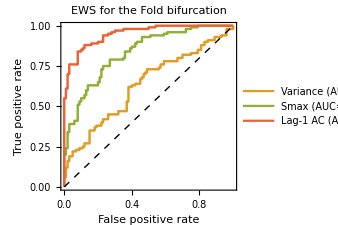

```mathematica
plotFold=ListPlot[{rocPlotDataVar,rocPlotDataSmax,rocPlotDataAc},
Joined->True,
Frame->frStyle,
ImageSize->imgs,
LabelStyle->ls,
PlotStyle->Evaluate[{colDict[#],Thickness[lt]}&/@labels],
FrameLabel->{{"True positive rate",None},{"False positive rate",None}},
AspectRatio->aRatio,
PlotLabel->"EWS for the Fold bifurcation",
ImageSize->imgs,
PlotLegends->Placed[legend,Scaled[{0.7,0.2}]],
Epilog->{Dashed,Line[{{0,0},{1,1}}]}]
```

## ROC for Flip

```mathematica
dfRocFlip[[1]]
```

{,fpr,tpr,thresholds,auc,ews}

```mathematica
(* Partition into different EWS *)
{dfRocVar,dfRocAc,dfRocSmax}=Prepend[Cases[dfRocFlip,{_,_,_,_,_,#}],dfRocFlip[[1]]]&/@{"Variance","Lag-2 AC","Smax"};
```

```mathematica
(* AUC scores *)
aucVar=dfRocVar[[2,5]];
aucAc=dfRocAc[[2,5]];
aucSmax=dfRocSmax[[2,5]];
aucScores={aucVar,aucAc,aucSmax};
```

```mathematica
labels={"Variance","Smax","Lag-2 AC"};
legend=LineLegend[colDict[#]&/@labels,Table[legLabel[x],{x,Transpose[{labels,aucScores}]}],Spacings->0.2]
```

```mathematica
rocPlotDataVar=dfRocVar[[2;;,{2,3}]];
rocPlotDataAc=dfRocAc[[2;;,{2,3}]];
rocPlotDataSmax=dfRocSmax[[2;;,{2,3}]];
```

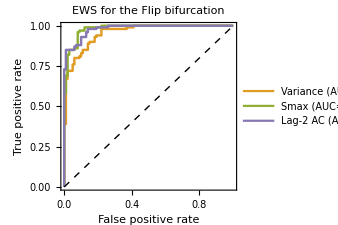

```mathematica
plotFlip=ListPlot[{rocPlotDataVar,rocPlotDataSmax,rocPlotDataAc},
Joined->True,
Frame->frStyle,
LabelStyle->ls,
FrameLabel->{{"True positive rate",None},{"False positive rate",None}},
PlotStyle->Evaluate[{colDict[#],Thickness[lt]}&/@labels],
AspectRatio->aRatio,
PlotLabel->"EWS for the Flip bifurcation",
ImageSize->imgs,
PlotLegends->Placed[legend,Scaled[{0.7,0.2}]],
Epilog->{Dashed,Line[{{0,0},{1,1}}]}]
```

## Grid plot

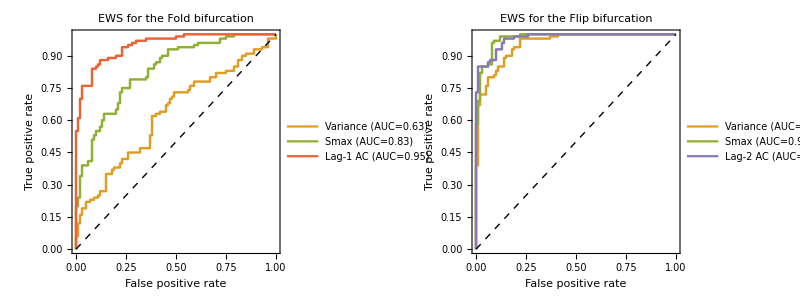

```mathematica
rocPlot=Grid[{{plotFold,plotFlip}}]
```

```mathematica
(*Export["figures/roc_plot_ricker.png",rocPlot];*)
```